```mathematica
vSATs = RandomVariate[NormalDistribution[1400,280],1000];
```

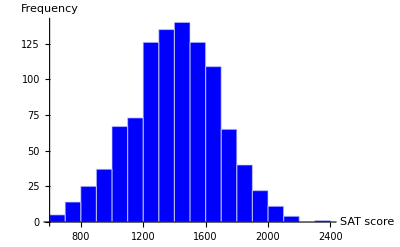

```mathematica
Histogram[vSATs,PlotRange->{{600,2400},Automatic},ChartStyle->{Blue},AxesLabel->{"SAT score","Frequency"},BaseStyle->{FontSize->16}]
```

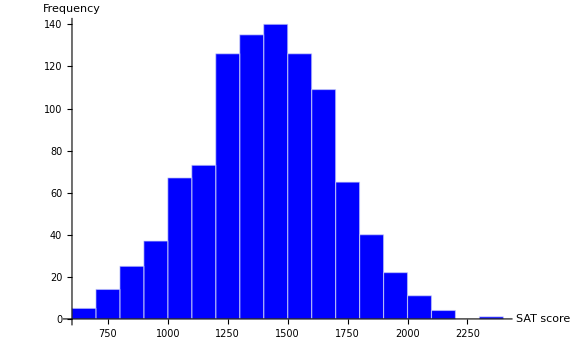

```mathematica
Show[%147,ImageSize->Large]
```

```mathematica
Mean[vSATs]
```

1404.62

```mathematica
Variance[vSATs]
```

79715.6

```mathematica
Sqrt[Variance[vSATs]]
```

282.34

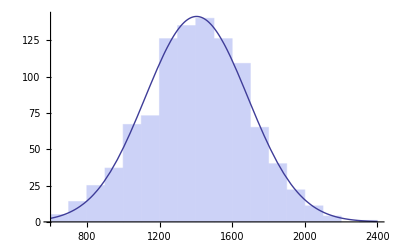

```mathematica
Show[Histogram[vSATs,PlotRange->{{600,2400},Automatic},ChartStyle->{Blue},AxesLabel->{"SAT score","Frequency"},BaseStyle->{FontSize->16}],Plot[100000*PDF[NormalDistribution[1404,282.34],x],{x,600,2400}]]
```

```mathematica
PDF
```